# SymQM软件文档

王程飞 
Sunday 09 January 2011

## 辅助函数

### 标量调和平均数

#### Code

```mathematica
(*avgScalar calculates the Harmonic Mean of a list of scalar values,but without the n times coefficient,i.e.HarmonicMean[para]/Length[para].*)avgScalar[para_List]:=1/Total[1/#&/@para];
```

#### Information

编号 : 
输入 : 标量列表para_List
输出 :调和平均即各标量的倒数和的倒数

#### Example

```mathematica
avgScalar[{1,2,3}]
```

6/11

### 失量加权平均数

#### Code

```mathematica
(*avgVector calculates the weighted mean of a list of vectors.*)avgVector[para_List]:=Module[{scalar},((scalar=Part[para,All,1]).Part[para,All,2])/Total[scalar]];
```

#### Information

编号 : 
输入 : {权重, 失量}元素组成的列表para_List
输出 :权重平均值

#### Example

```mathematica
avgVector[{{2,{3,5,6}},{4,{2,1,1}}}]
```

{7/3,7/3,8/3}

### 角动量索引顺序

#### Code

```mathematica
(*"Angular Momentum" Indices*)
LS={{0,0,0}};
LP={{1,0,0},{0,1,0},{0,0,1}};
LD={{2,0,0},{0,2,0},{0,0,2},{1,1,0},{1,0,1},{0,1,1}};
LF={{3,0,0},{0,3,0},{0,0,3},{1,2,0},{2,1,0},{2,0,1},{1,0,2},{0,1,2},{0,2,1},{1,1,1}};
LG={{4,0,0},{0,4,0},{0,0,4},{3,1,0},{3,0,1},{0,3,1},{1,3,0},{0,1,3},{1,0,3},{2,2,0},{2,0,2},{0,2,2},{2,1,1},{1,2,1},{1,1,2}};
LH={{5,0,0},{0,5,0},{0,0,5},{4,1,0},{4,0,1},{0,4,1},{1,4,0},{0,1,4},{1,0,4},{3,2,0},{3,0,2},{0,3,2},{2,3,0},{0,2,3},{2,0,3},{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2}};
LL={LS,LP,LD,LF,LG(*,LH*)};
LLflat=Flatten[LL,1];
IP[l_]:=Position[LLflat,l][[1,1]];
LLpair=Flatten[Table[{LLflat[[l1]],LLflat[[l2]]},{l1,Length[LLflat]},{l2,l1}],1];
IP[l1_,l2_]:=Position[LLpair,{l1,l2}][[1,1]];
IQ[i_]:=LLflat[[i]];
```

#### Information

名称 : IP
输入 :一个三维的角动量l, 或者一对三维角动量 l1, l2
输出 :给出顺序索引, 即在各种不重复的三维的角动量的列表中,属于第几个, 或者在各对不重复的三维的角动量的列表中属于第几对
依赖: LLflat, LLpair

#### Theorem

Position会返回一个列表, 其中的每个元素又是表示层次位置的一个列表, 故采用[[1,1]]方便的去除两层括号{{16}}. 对一个三维角动量次数的索引, 通过Position在LLflat定位符合的三维角动量排序, 对一对角动量, 则在LLpair中定位. LLpair是由LLflat生成的有序对, 由于乘积因子是可交换的, 为了减去左右对称造成的积分计算重复, 在一对角动量中规定l1>l2, 后者的次序范围不超过前者, 这样LLflat组合后生成的LLpair不会重复. IP是由角动量查顺序索引, IQ是由顺序查角动量

#### Example

```mathematica
IP[{2,0,1}]
IP[{2,0,1},{0,0,0}]
IP[{0,0,0},{2,0,1}]
```

16

121

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

### 归一化

#### Code

```mathematica
NormFactor[α_,l_List]:=Module[{t=Total[l]},1/(√Times@@(Product[2 i-1,{i,#}]&/@l)) 2^t α^((2 t+3)/4) (2/π)^(3/4)];
```

#### Information

名称 : 
输入 :
输出 :
依赖:

#### Theorem

对<a|a>高斯基函数自乘求出的结果分析如下.

<a|a>=∫(x-p1_x)^l1_x(y-p1_y)^l1_y(z-p1_z)^l1_z exp[-α_1(r-p1)^2](x-p1_x)^l1_x(y-p1_y)^l1_y(z-p1_z)^l1_z exp[-α_1(r-p1)^2]ⅆr 
=∫(x-p1_x)^(2 l1_x)(y-p1_y)^(2 l1_y)(z-p1_z)^(2 l1_z)exp[-2 α_1(r-p1)^2]ⅆr
=∫_(-∞)^(+∞) (x-p1_x)^(2 l1_x)exp[-2 α_1(x-p1_x)^2]ⅆx∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=∫_(-∞)^(+∞) (x-p1_x)^(2 l1_x)exp[-2 α_1(x-p1_x)^2]ⅆ(x-p1_x)∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=2∫_0^(+∞) (x-p1_x)^(2 l1_x)exp[-2 α_1(x-p1_x)^2]ⅆ(x-p1_x)∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=2∫_0^(+∞) 1/(4 α_1)(x-p1_x)^(2 l1_x-1)exp[-2 α_1(x-p1_x)^2]ⅆ(2 α_1(x-p1_x)^2)∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=∫_0^(+∞) 1/(2 α_1)1/(2 α_1)^(l1_x-1/2)(2 α_1(x-p1_x)^2)^(l1_x-1/2)exp[-2 α_1(x-p1_x)^2]ⅆ(2 α_1(x-p1_x)^2)∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=1/(2 α_1)^(l1_x+1/2)∫_0^(+∞) (2 α_1(x-p1_x)^2)^(l1_x+1/2-1)exp[-2 α_1(x-p1_x)^2]ⅆ(2 α_1(x-p1_x)^2)∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz

对于gamma函数我们知道

Γ(z)=∫_0^∞ t^(z-1)e^-t dt

所以可以得到

<a|a>=1/(2 α_1)^(l1_x+1/2)Γ(l1_x+1/2)∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=1/(2 α_1)^(l1_x+1/2)Γ((2 l1_x+1)/2)∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=^-1/(2 α_1)^(l1_x+1/2)((2 l1_x-1)!!)/2^l1_x∫_(-∞)^(+∞) (y-p1_y)^(2 l1_y)exp[-2 α_1(y-p1_y)^2]ⅆy∫_(-∞)^(+∞) (z-p1_z)^(2 l1_z)exp[-2 α_1(z-p1_z)^2]ⅆz
=1/(2 α_1)^(l1_x+1/2)((2 l1_x-1)!!)/2^l1_x √π 1/(2 α_1)^(l1_y+1/2)((2 l1_y-1)!!)/2^l1_y √π 1/(2 α_1)^(l1_z+1/2)((2 l1_z-1)!!)/2^l1_z √π
=(π/(2 α_1))^(3/2)((2 l1_x-1)!!(2 l1_y-1)!!(2 l1_z-1)!!)/(4 α_1)^(l1_x+l1_y+l1_z)

所以可以进一步得到归一化系数

((2 α_1)/π)^(3/4)((4 α_1)^(l1_x+l1_y+l1_z)/((2 l1_x-1)!!(2 l1_y-1)!!(2 l1_z-1)!!))^(1/2)

#### Example

```mathematica
IP[{2,0,1}]
IP[{2,0,1},{0,0,0}]
IP[{0,0,0},{2,0,1}]
```

16

121

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

### 不完全Gamma函数

#### Code

```mathematica
auxFF[m_Integer,T_]:=auxFF[m,T]=(1/2) (T)^(-m-1/2) (Gamma[1/2+m]-Gamma[1/2+m,T]);
```

#### Information

名称 : 
输入 :
输出 :
依赖:

#### Theorem

对于gamma函数我们有定义：

Γ(z)=∫_0^∞ t^(z-1)e^-t dt

此外，不完全gamma函数的积分定义表达为：

Γ(a,z)=∫_z^∞ t^(a-1)e^-t dt

在m为非负整数，且T非零的情况下，量化计算中的Fm(T)本质就是半整数阶函数，关系式如下：

F_m(T)=∫_0^1 t^(2m)e^(-T t^2)ⅆt=(Γ(m+1/2)-Γ(m+1/2,T))/(2 T^(m+1/2))

当T逼近于0时，可以证明，该公式的极限为1/(1 + 2 m)

```mathematica
Limit[1/2 T^(-(1/2)-m) (Gamma[1/2+m]-Gamma[1/2+m,T]),T->0]
```

1/(1+2 m)

但0／0型的数值计算会遇到稳定性的问题，如图可以看到当接近出现波动。

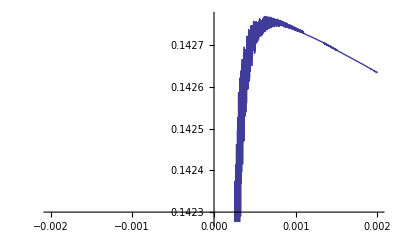

```mathematica
AuxFF[m_Integer,T_]:=1/2 T^(-(1/2)-m) (Gamma[1/2+m]-Gamma[1/2+m,T]);
Plot[AuxFF[3,t],{t,-0.002,0.002}]
```

#### Example

```mathematica
IP[{2,0,1}]
IP[{2,0,1},{0,0,0}]
IP[{0,0,0},{2,0,1}]
```

16

121

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

## 重叠积分计算

### 乘积原理

#### Code

```mathematica
(* Initialization for the two GTOs product, (00): The Kernel Function
*)
GIP[{α1_, {0, 0, 0}, p1_List}, {α2_, {0, 0, 0}, 
    p2_List}] := 
  GIP[{α1, {0, 0, 0}, p1}, {α2, {0, 0, 0}, p2}] = 
   Block[{α = avgScalar[{α1, α2}]}, (Pi/(α1 + α2))^(3/2) Exp[-α (p1 - p2).(p1 - p2)]];
```

#### Information

编号 : 
输入 : 两个角动量都为{0,0,0}的高斯基函数的指数参数α1, α2, 和两个中心位置参数p1_List, p2_List
输出 : 两个1s型的高斯基函数积分值
依赖 : avgScalar

#### Theorem

根据高斯乘积原理， 两个1s型的高斯基函数乘积，得到一个新的高斯基函数, 即有

|0_A>=exp[-α_1(r-p1)^2],|0_B>=exp[-α_2(r-p2)^2]

相乘得

|0_A 0_B>
=exp[-α_1(r-p1)^2-α_2(r-p2)^2]
=exp[-α_1(r^2-2rp1+p1^2)-α_2(r^2-2rp2+p2^2)]
=exp[-(α_1+α_2)(r^2-2r(α_1 p1+α_2 p2)/(α_1+α_2)+(α_1 p1^2+α_2 p2^2)/(α_1+α_2))]

如果令

P=(α_1 p1+α_2 p2)/(α_1+α_2)
|0_A 0_B>
=exp[-(α_1+α_2)(r^2-2rP+P^2-P^2+(α_1 p1^2+α_2 p2^2)/(α_1+α_2))]
=exp[-(α_1+α_2)(r-P)^2]exp[-1/(1/α_1+1/α_2)(p1-p2)^2]

故在积分中则易知

<0_A|0_B>=∫exp[-(α_1+α_2)(x-P_x)^2]ⅆx ∫exp[-(α_1+α_2)(y-P_y)^2]ⅆy∫exp[-(α_1+α_2)(z-P_z)^2]ⅆz exp[-1/(1/α_1+1/α_2)(p1-p2)^2]

由欧拉积分, 咖马函数的性质可知

∫_(-∞)^(+∞) e^(-αx^2)ⅆx=1/(√α)∫_(-∞)^(+∞) e^(-(√α x)^2)ⅆ(√α x)=2/(√α)∫_0^∞ e^(-(√α x)^2)ⅆ(√α x)=√(π/α)=1/(√α)Γ[1/2]

所以(1)式为

<0_A|0_B>=(√(π/(α_1+α_2)))^3 exp[-1/(1/α_1+1/α_2)(p1-p2)^2]

#### Example

```mathematica
GIP[{1,{0,0,0},{0.8,0,0}},{0.6,{0,0,0},{-0.8,0,0}}]
```

1.05347

### 重叠积分递归关系

#### Code

```mathematica
AuxF[i_Integer,{α1_,l1_List,p1_List},{α2_,l2_List,p2_List}]:=Block[{unit=Unit[i]},(avgVector[{{α1,p1},{α2,p2}}]-p1)[[i]] GIP[{α1,l1-unit,p1},{α2,l2,p2}]+(l1[[i]] GIP[{α1,l1-2 unit,p1},{α2,l2,p2}]+l2[[i]] GIP[{α1,l1-unit,p1},{α2,l2-unit,p2}])/(2 (α1+α2))];
```

#### Information

编号 : 
输入 : 对第i_Integer维分量进行降次数操作, 两个高斯函数指数参数α1, α2, 中心位置参数p1_List, p2_List, 角动量 l1_List, l2_List
输出 : 
依赖 : 其他GIP Unit

#### Theorem

一般的两个高斯函数的重叠积分可写为

<a|b>=∫(x-p1_x)^l1_x(y-p1_y)^l1_y(z-p1_z)^l1_z exp[-α_1(r-p1)^2](x-p2_x)^l2_x(y-p2_y)^l2_y(z-p2_z)^l2_z exp[-α_2(r-p2)^2]ⅆr

(3)可视为三个分量因子的乘积, 每一个因子都如下(以x分量为例, 其余y, z类似)

∫_(-∞)^(+∞) (x-p1_x)^l1_x(x-p2_x)^l2x×exp(-α_1(x-p1_x)^2-α_2(x-p2_x)^2)ⅆx
=exp(-(α_1 p1_x^2+α_2 p2_x^2))×∫_(-∞)^(+∞) (x-p1_x)^l1_x(x-p2_x)^l2x exp(-(α_1+α_2)x^2+2(α_1 p1_x+α_2 p2_x)x)ⅆx

同样令

P=(α_1 p1+α_2 p2)/(α_1+α_2)

则代入(4) 可得

∫_(-∞)^(+∞) (x-p1_x)^l1_x(x-p2_x)^l2x×exp(-α_1(x-p1_x)^2-α_2(x-p2_x)^2)ⅆx
=exp(-(α_1 p1_x^2+α_2 p2_x^2))×∫_(-∞)^(+∞) (x-p1_x)^l1_x(x-p2_x)^l2x exp(-(α_1+α_2)(x^2-2 P_x x+P_x^2-P_x^2))ⅆx

再利用换元法, 令 x'=x-P_x, 代入上式得

exp((α_1+α_2)P_x^2-(α_1 p1_x^2+α_2 p2_x^2))×∫_(-∞)^(+∞) (x'+P_x-p1_x)^l1_x(x'+P_x-p2_x)^l2x exp(-(α_1+α_2)(x')^2)ⅆx'

重新将x’记为x, 由上式得

exp((α_1+α_2)P_x^2-(α_1 p1_x^2+α_2 p2_x^2))×∫_(-∞)^(+∞) (x+P_x-p1_x)^l1_x(x+P_x-p2_x)^l2x exp(-(α_1+α_2)x^2)ⅆx

故每个(4)式可化为(5). 进一步, 可把(5)看成两个部分乘积, k_x×I_x的形式.
对于(5)式后面一项, 即积分部分I_x, 用二项式定理展开可得

∫_(-∞)^(+∞) (x+P_x-p1_x)^l1_x(x+P_x-p2_x)^l2x exp(-(α_1+α_2)x^2)ⅆx
=∑_(k_1=0)^l1_x ∑_(k_2=0)^l2_x (l1_x
k_1)(l2_x
k_2)×(P_x-p1_x)^(l1-k_1)(P_x-p2_x)^(l2-k_2)×∫_(-∞)^(+∞) x^(k_1+k_2)exp(-(α_1+α_2)x^2)ⅆx

如果k_1+k_2为奇数, 那么在对称的积分区间上总值为0. 
如果k_1+k_2为偶数, 利用分部积分展开(6)中的积分部分得

∫_(-∞)^(+∞) x^(k_1+k_2)exp(-(α_1+α_2)x^2)ⅆx
=-1/(2(α_1+α_2))∫_(-∞)^(+∞) x^(k_1+k_2-1)ⅆexp(-(α_1+α_2)x^2)
=-1/(2(α_1+α_2))[x^(k_1+k_2-1)exp(-(α_1+α_2)x^2)|_(-∞)^(+∞)-(k_1+k_2-1)∫_(-∞)^(+∞) x^(k_1+k_2-2)exp(-(α_1+α_2)x^2)ⅆx]

已知α_1+α_2都是正数, 由罗比塔法则易知exp(-(α_1+α_2)x^2)衰减比x^(k_1+k_2-1)快, 故取极限后值为0, 上式化为

-1/(2(α_1+α_2))[x^(k_1+k_2-1)exp(-(α_1+α_2)x^2)|_(-∞)^(+∞)-(k_1+k_2-1)∫_(-∞)^(+∞) x^(k_1+k_2-2)exp(-(α_1+α_2)x^2)ⅆx]
=-1/(2(α_1+α_2))[0-0-(k_1+k_2-1)∫_(-∞)^(+∞) x^(k_1+k_2-2)exp(-(α_1+α_2)x^2)ⅆx]
=(k_1+k_2-1)/(2(α_1+α_2))∫_(-∞)^(+∞) x^(k_1+k_2-2)exp(-(α_1+α_2)x^2)ⅆx

重复上述过程, 总共经过(k_1+k_2)/2次分部积分, 再由欧拉积分可得

((k_1+k_2-1)!!)/(2(α_1+α_2))^((k_1+k_2)/2)∫_(-∞)^(+∞) exp(-(α_1+α_2)x^2)ⅆx
=((k_1+k_2-1)!!)/(2(α_1+α_2))^((k_1+k_2)/2)√(π/(α_1+α_2))

将(7)代回(6)可得I_x的最终形式

∑_(k_1=0)^l1_x ∑_(k_2=0)^l2_x (l1_x
k_1)(l2_x
k_2)×(P_x-p1_x)^(l1-k_1)(P_x-p2_x)^(l2-k_2)×((k_1+k_2-1)!!)/(2(α_1+α_2))^((k_1+k_2)/2)√(π/(α_1+α_2))

将三个(5)式的k部分提取合并可得

k_(a,b)=k_x k_y k_z
=exp((α_1+α_2)P_x^2-(α_1 p1_x^2+α_2 p2_x^2)+(α_1+α_2)P_y^2-(α_1 p1_y^2+α_2 p2_y^2)+(α_1+α_2)P_z^2-(α_1 p1_z^2+α_2 p2_z^2))
=exp((α_1+α_2)P^2-(α_1 p1^2+α_2 p2^2))

因此将三个类似(4)式的分量因式相乘, (3)最终可化为

<a|b>=k_(a,b)I_x I_y I_z

其中k_(a,b)由(9)所表示, I_x如(8)所示, 其余I_y, I_z类似. 
接下来的推导对(3)求导的结果. 先对(9)指数exp内部分求p1_i偏微分, 以p1_x为例, 可得

2(α_1+α_2)P_x(α_1/(α_1+α_2))-2 α_1 p1_x
=2 α_1(P_x-p1_x)

类似的y, z可知. 综合得

1/(2 α_1)∂/(∂p1_i)k_(a,b)=(P_x-p1_x)k_(a,b)

根据组合的定义, 易知

(l1_i
k_1)(l1_i-k_1)=(l1_i(l1_i-1)...(l1_i-k_1+1))/(k_1!)(l1_i-k_1)
=l1_i((l1_i-1)...(l1_i-k_1+1)(l1_i-1-k_1+1))/(k_1!)=l1_i(l1_i-1
k_1)

另外, 为了方便起见, 将只含 k_1, k_2变量的部分单独替换为

V(k)=((k_1+k_2-1)!!)/(2(α_1+α_2))^((k_1+k_2)/2)√(π/(α_1+α_2))

利用(11), (12)可以对(8)求篇微分

(∂I_i)/(∂p1_i)=∑_(k_1=0)^(l1_i-1) ∑_(k_2=0)^l2_i l1_i(l1_i-1
k_1)(l2_i
k_2)×(α_1/(α_1+α_2)-1)(P_i-p1_i)^(l1-k_1-1)(P_i-p2_i)^(l2-k_2)×V(k)
+∑_(k_1=0)^l1_i ∑_(k_2=0)^(l2_i-1) l2_i(l1_i
k_1)(l2_i-1
k_2)×(α_1/(α_1+α_2))(P_i-p1_i)^(l1-k_1)(P_i-p2_i)^(l2-k_2-1)×V(k)

利用I符号来记录, 可得

1/(2 α_1)(∂I_i)/(∂p1_i)=l1_i(1/(2(α_1+α_2))-1/(2 α_1))I_i(l1_i-1, l2_i)+l2_i/(2(α_1+α_2))I_i(l1_i, l2_i-1)

对于(3)的两个基函数, 令

ψ(r,α_1,l1,p1)=(x-p1_x)^l1_x(y-p1_y)^l1_y(z-p1_z)^l1_z exp[-α_1(r-p1)^2]

对其求篇微分得

∂/(∂p1_i)ψ(r,α_1,l1,p1)=2 α_1 ψ(r,α_1,l1_i+1_i,p1)-l1_i ψ(r,α_1,l1_i-1_i,p1)

即有

ψ(r,α_1,l1_i+1_i,p1)=1/(2 α_1)∂/(∂p1_i)ψ(r,α_1,l1,p1)+l1_i/(2 α_1)ψ(r,α_1,l1_i-1_i,p1)

那么根据(3)式可得

<a+1_i|b>=∫ⅆr 1/(2 α_1)∂/(∂p1_i)ψ(r,α_1,l1,p1)ψ(r,α_2,l2,p2)+l1_i/(2 α_1)ψ(r,α_1,l1_i-1_i,p1)ψ(r,α_2,l2,p2)
=1/(2 α_1)∂/(∂p1_i)<a|b>+l1_i/(2 α_1)<a-1_i|b>

将(13)与(10)代入(15)可得, 并不失一般性i取x

<a+1_x|b>=(P_x-p1_x)<a|b>+k_(a,b)(l1_x(1/(2(α_1+α_2))-1/(2 α_1))I_x(l1_x-1, l2_x)+l2_x/(2(α_1+α_2))I_x(l1_x, l2_x-1))×I_y×I_z+l1_x/(2 α_1)<a-1_x|b>
=(P_x-p1_x)<a|b>+l1_x/(2(α_1+α_2))k_(a,b)×I_x(l1_x-1, l2_x)×I_y×I_z+l2_x/(2(α_1+α_2))I_x(l1_x, l2_x-1)×I_y×I_z
=(P_x-p1_x)<a|b>+l1_x/(2(α_1+α_2))<a-1_x|b>+l2_x/(2(α_1+α_2))<a|b-1_x>

根据对称性最终可得递推公式

<a+1_i|b>=(P_i-p1_i)<a|b>+l1_i/(2(α_1+α_2))<a-1_i|b>+l2_i/(2(α_1+α_2))<a|b-1_i>

#### Example

```mathematica
GIP[{1,{0,0,0},{0.8,0,0}},{0.6,{0,0,0},{-0.8,0,0}}]
```

1.05347

## 动能积分计算

### 动能积分与重叠积分的关系

#### Code

```mathematica
FunPrimKin[{α1_,l1_List,p1_List},{α2_,l2_List,p2_List}]:=FunPrimKin[{α1,l1,p1},{α2,l2,p2}]=ConstrainedSimplify[(-1/2) Sum[D[FunPrimOvl[{α1,l1,p1},{α2,l2,p2}],{p2[[i]],2}],{i,3}]];
```

#### Information

编号 : 
输入 : 两个角动量都为{0,0,0}的高斯基函数的指数参数α1, α2, 和两个中心位置参数p1_List, p2_List
输出 : 两个1s型的高斯基函数积分值
依赖 : avgScalar

#### Theorem

根据(14)可知, r-p1总是成对出现, 完全对称, 只是相差一个正负号而已, 所以可以得到

∂/(∂r_i)ψ(r,α_1,l1,p1)=-∂/(∂p1_i)ψ(r,α_1,l1,p1)

求导的结果仍然是r-p1成对出现, 所以可得

∂^2/(∂r_i^2)ψ(r,α_1,l1,p1)=∂^2/(∂p1_i^2)ψ(r,α_1,l1,p1)

所以则动能积分可以通过求重叠积分的导数来获得

<a|-1/2∇^2|b>=-1/2<a|∇_x^2 +∇_y^2 +∇_z^2|b>=-1/2<a|∇_p2_x^2 +∇_p2_y^2 +∇_p2_z^2|b>=-1/2∇_p2^2<a|b>

#### Example

```mathematica
avgScalar[{1,2,3}]
```

6/11

## 核吸引积分计算

### 核吸引积分递归关系

#### Code

```mathematica
(*Symmetical w.r.t the exchange of a and b.*)AuxN[i_Integer,m_Integer,{α1_,l1_List,p1_List},{α2_,l2_List,p2_List},p3_List]:=Module[{unit=Unit[i],p=avgVector[{{α1,p1},{α2,p2}}],α=α1+α2},(p[[i]]-p1[[i]]) NAI[m,{α1,l1-unit,p1},{α2,l2,p2},p3]-(p[[i]]-p3[[i]]) NAI[m+1,{α1,l1-unit,p1},{α2,l2,p2},p3]+(1/(2 α)) l1[[i]] (NAI[m,{α1,l1-2 unit,p1},{α2,l2,p2},p3]-NAI[m+1,{α1,l1-2 unit,p1},{α2,l2,p2},p3])+(1/(2 α)) l2[[i]] (NAI[m,{α1,l1-unit,p1},{α2,l2-unit,p2},p3]-NAI[m+1,{α1,l1-unit,p1},{α2,l2-unit,p2},p3])];
```

#### Information

编号 : 
输入 : 两个角动量都为{0,0,0}的高斯基函数的指数参数α1, α2, 和两个中心位置参数p1_List, p2_List
输出 : 两个1s型的高斯基函数积分值
依赖 : avgScalar

#### Theorem

根据上文重叠积分的Theorem部分, 可对三个高斯基函数乘积作类似的推导, 从而获得与(16)类似的递推关系

<a+1_i|c|b>=(G_i-p1_i)<a|c|b>+l1_i/(2(α_1+α_2+α_3))<a-1_i|c|b>+l2_i/(2(α_1+α_2+α_3))<a|c|b-1_i>+l3_i/(2(α_1+α_2+α_3))<a|c-1_i|b>

这里G_i为

G=(α_1 p1+α_2 p2+α_3 p3)/(α_1+α_2+α_3)

那么借用(14)的记法, 核吸引积分(未显示核电荷)可表示为

[a|b]=<a|b>^(0)=∫ψ(r,α_1,l1,p1)1/(|r-p3|)ψ(r,α_2,l2,p2)ⅆr
=2/π^(1/2)∫_0^∞ ⅆu∫ψ(r,α_1,l1,p1)exp(-u^2(r-p3)^2)ψ(r,α_2,l2,p2)ⅆr=2/π^(1/2)∫_0^∞ ⅆu(a|0|b)

故可将上式看作三个高斯基函数乘积, 中间的为s型, 可以利用(17)推导出关系式

<a+1_i|0|b>=(G_i-p1_i)<a|0|b>+l1_i/(2(α_1+α_2+u^2))<a-1_i|0|b>+l2_i/(2(α_1+α_2+u^2))<a|0|b-1_i>

令α=α_1+α_2则上式化为

(αP_i/(α+u^2)+(u^2 p1_i)/(α+u^2)-p1_i)<a|0|b>+l1_i/(2α)(α/(α+u^2))<a-1_i|0|b>+l2_i/(2α)(α/(α+u^2))<a|0|b-1_i>
=((1-u^2/(α+u^2))P_i+(u^2 p1_i)/(α+u^2)-p1_i)<a|0|b>+l1_i/(2α)(1-u^2/(α+u^2))<a-1_i|0|b>+l2_i/(2α)(1-u^2/(α+u^2))<a|0|b-1_i>
=(P_i-p1_i)<a|0|b>-(u^2/(α+u^2))(P_i-p1_i)<a|0|b>+l1_i/(2α)(1-u^2/(α+u^2))<a-1_i|0|b>+l2_i/(2α)(1-u^2/(α+u^2))<a|0|b-1_i>

定义辅助核吸引积分

<a｜b>^(m)=2/π^(1/2)∫_0^∞ ⅆu(u^2/(α+u^2))^m<a|0|b>

定义根据(18)可得到

<a+1_i|b>^(m)=(P_i-p1_i)<a|b>^(m)-(P_i-p1_i)<a|b>^(m+1)+l1_i/(2α)(<a-1_i|b>^(m)-<a-1_i|b>^(m+1))+l2_i/(2α)(<a|b-1_i>^(m)-<a|b-1_i>^(m+1))

调整a+1_i为a得到

<a|b>^(m)=(P_i-p1_i)<a-1_i|b>^(m)-(P_i-p1_i)<a-1_i|b>^(m+1)+l1_i/(2α)(<a-2_i|b>^(m)-<a-2_i|b>^(m+1))+l2_i/(2α)(<a-1_i|b-1_i>^(m)-<a-1_i|b-1_i>^(m+1))

#### Example

```mathematica
avgScalar[{1,2,3}]
```

6/11

## 双电子积分计算

### 双电子积分递归关系

#### Code

```mathematica
(*Auxciliary definition for VRR*)AuxF[i_Integer,m_Integer,{α1_,l1_List,p1_List},{α2_,l2_List,p2_List},{α3_,l3_List,p3_List},{α4_,l4_List,p4_List}]:=Module[{unit=Unit[i],p=avgVector[{{α1,p1},{α2,p2}}],q=avgVector[{{α3,p3},{α4,p4}}],α=α1+α2,β=α3+α4,γ=avgScalar[{α1+α2,α3+α4}]},(p[[i]]-p1[[i]]) ERI[m,{α1,l1-unit,p1},{α2,l2,p2},{α3,l3,p3},{α4,l4,p4}]+(avgVector[{{α,p},{β,q}}][[i]]-p[[i]]) ERI[m+1,{α1,l1-unit,p1},{α2,l2,p2},{α3,l3,p3},{α4,l4,p4}]+(l1[[i]]/(2 α)) (ERI[m,{α1,l1-2 unit,p1},{α2,l2,p2},{α3,l3,p3},{α4,l4,p4}]-(β/(α+β)) ERI[m+1,{α1,l1-2 unit,p1},{α2,l2,p2},{α3,l3,p3},{α4,l4,p4}])+(l2[[i]]/(2 α)) (ERI[m,{α1,l1-unit,p1},{α2,l2-unit,p2},{α3,l3,p3},{α4,l4,p4}]-(β/(α+β)) ERI[m+1,{α1,l1-unit,p1},{α2,l2-unit,p2},{α3,l3,p3},{α4,l4,p4}])+(l3[[i]]/(2 (α+β))) ERI[m+1,{α1,l1-unit,p1},{α2,l2,p2},{α3,l3-unit,p3},{α4,l4,p4}]+(l4[[i]]/(2 (α+β))) ERI[m+1,{α1,l1-unit,p1},{α2,l2,p2},{α3,l3,p3},{α4,l4-unit,p4}]];
```

#### Information

编号 : 
输入 : 两个角动量都为{0,0,0}的高斯基函数的指数参数α1, α2, 和两个中心位置参数p1_List, p2_List
输出 : 两个1s型的高斯基函数积分值
依赖 : avgScalar

#### Theorem

同样借用(14)核吸引积分可以表示为

[ab|cd]=∫ⅆ r_1ⅆ r_2ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)1/(|r_1-r_2|)ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)
=∫ⅆ r_1ⅆ r_2ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)2/(√π)∫_0^∞ ⅆu exp(-(r_1-r_2)^2 u^2)ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)
=2/(√π)∫_0^∞ ⅆu∫ⅆ r_1ⅆ r_2ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)exp(-(r_1-r_2)^2 u^2)ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)
=2/(√π)∫_0^∞ ⅆu<ab|u|cd>
=2/(√π)∫_0^∞ ⅆu∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)<a|0_r_2|b>

这样双电子排斥积分就与三高斯基函数乘积有关, 可以利用相应的性质推导递推关系. 根据(17)可以同样获得在c上降低角动量的递推关系式

<a|c+1_i|b>=(G_i-r_1_i)<a|c|b>+l1_i/(2(α_1+α_2+α_3))<a-1_i|c|b>+l2_i/(2(α_1+α_2+α_3))<a|c|b-1_i>+l3_i/(2(α_1+α_2+α_3))<a|c-1_i|b>

此处令 β=α_3+α_4, Q=α_3 p3+α_4 p4, 则有

<c|1_i_r1|d>=(G_i-r_1_i)<c|0_i_r1|d>+l3_i/(2(β+u^2))<c-1_i|0_i_r1|d>+l4_i/(2(β+u^2))<c|0_i_r1|d-1_i>
=((βQ_i+u^2 r_1_i)/(β+u^2)-r_1_i)<c|0_i_r1|d>+l3_i/(2(β+u^2))<c-1_i|0_i_r1|d>+l4_i/(2(β+u^2))<c|0_i_r1|d-1_i>
=(β(Q_i-r_1_i))/(β+u^2)<c|0_i_r1|d>+l3_i/(2(β+u^2))<c-1_i|0_i_r1|d>+l4_i/(2(β+u^2))<c|0_i_r1|d-1_i>

可以写成下面的形式, 以便之后的推导使用到

u^2<c|1_i_r1|d>=β(Q_i-r_1_i)<c|0_i_r1|d>+l3_i/2<c-1_i|0_i_r1|d>+l4_i/2<c|0_i_r1|d-1_i>-β<c|1_i_r1|d>

由(17)知

<a+1_i|0_r_2|b>=(G_i-A_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>
=((αP_i+u^2 r_(2_i))/(α+u^2)-A_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>
=(-α/(α+u^2)(r_(2_i)-P_i)+P_i-A_i+r_(2_i)-P_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>
=(u^2/(α+u^2))(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>

需要将上式与β联系起来, 故引入变量ρ

ρ=αβ/(α+β)

代入(21)得

<a+1_i|0_r_2|b>=(u^2(α+β)/(αβ+αu^2+βu^2)(αβ+αu^2+βu^2)/(α+β)1/(α+u^2))(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>
=(u^2/(ρ+u^2)(αβ+αu^2+βu^2)/((α+β)(α+u^2)))(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>
=(u^2/(ρ+u^2)((αβ+βu^2)/((α+β)(α+u^2))+αu^2/((α+β)(α+u^2))))(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>
=(u^2/(ρ+u^2)β/(α+β)+u^2/(ρ+u^2)u^2/(α+β)α/(α+u^2))(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/(2(α+u^2))<a-1_i|0_r_2|b>+l2_i/(2(α+u^2))<a|0_r_2|b-1_i>

所以可以看出

u^2/(α+u^2)=u^2/(ρ+u^2)β/(α+β)+u^2/(ρ+u^2)α/(α+β)u^2/(α+u^2)

还可以得到

1/(α+u^2)=1/α α/(α+u^2)=1/α(1－u^2/(α+u^2))=1/α(1－u^2/(ρ+u^2)β/(α+β)-u^2/(ρ+u^2)α/(α+β)u^2/(α+u^2))=1/α(1－u^2/(ρ+u^2)ρ/α)-u^2/(ρ+u^2)1/(α+β)u^2/(α+u^2)

代入(22)可得

<a+1_i|0_r_2|b>=u^2/(ρ+u^2)β/(α+β)(r_(2_i)-P_i)<a|0_r_2|b>+u^2/(ρ+u^2)u^2/(α+β)α/(α+u^2)(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/2(1/α(1－u^2/(ρ+u^2)ρ/α)-u^2/(ρ+u^2)1/(α+β)u^2/(α+u^2))<a-1_i|0_r_2|b>+l2_i/2(1/α(1－u^2/(ρ+u^2)ρ/α)-u^2/(ρ+u^2)1/(α+β)u^2/(α+u^2))<a|0_r_2|b-1_i>

进一步的证明需要用到(19)推导出来的式子

-1/(α+β)u^2/(ρ+u^2)u^2<a|1_i_r2|b>=u^2/(α+β)u^2/(ρ+u^2)α/(α+u^2)(r_2_i-P_i)<a|0_i_r2|b>-u^2/(α+β)u^2/(ρ+u^2)1/(α+u^2)l1_i/2<a-1_i|0_i_r2|b>-u^2/(α+β)u^2/(ρ+u^2)1/(α+u^2)l2_i/2<a|0_i_r2|b-1_i>

代入(23)可以得到

<a+1_i|0_r_2|b>=u^2/(ρ+u^2)β/(α+β)(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i|0_r_2|b>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a|0_r_2|b-1_i> －1/(α+β)u^2/(ρ+u^2)u^2<a|1_i_r2|b>

对上式的最后一项乘上c, d基函数, 展开研究可以得到如下关系

－1/(α+β)u^2/(ρ+u^2)∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)u^2<a|1_i_r2|b>
=－1/(α+β)u^2/(ρ+u^2)∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)u^2∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,u^2,l,r_2)ψ(r_1,α_2,l2,p2)
=1/(α+β)u^2/(ρ+u^2)∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_1,u^2,l,r_1)ψ(r_2,α_4,l4,p4)u^2∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)
=1/(α+β)u^2/(ρ+u^2)∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)u^2<c|1_i_r1|d>

将(24)都乘上c, d的基函数, 并应用上式的关系, 可以得到

<a+1_i b|u|cd>
=∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)<a+1_i|0_r_2|b>
=∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)(
u^2/(ρ+u^2)β/(α+β)(r_(2_i)-P_i)<a|0_r_2|b>+(P_i-A_i)<a|0_r_2|b>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i|0_r_2|b>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a|0_r_2|b-1_i> －1/(α+β)u^2/(ρ+u^2)u^2<a|1_i_r2|b>)
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)u^2/(ρ+u^2)β/(α+β)(r_(2_i)-P_i)<a|0_r_2|b>-∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)1/(α+β)u^2/(ρ+u^2)u^2<a|1_i_r2|b>
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+u^2/(ρ+u^2)β/(α+β)∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)(r_(2_i)-P_i)<a|0_r_2|b>+1/(α+β)u^2/(ρ+u^2)∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)u^2<c|1_i_r1|d>

将最后一项用(20)代入可得

<a+1_i b|u|cd>
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+u^2/(ρ+u^2)β/(α+β)∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)(r_(2_i)-P_i)<a|0_r_2|b>+1/(α+β)u^2/(ρ+u^2)∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)(β(Q_i-r_1_i)<c|0_i_r1|d>+l3_i/2<c-1_i|0_i_r1|d>+l4_i/2<c|0_i_r1|d-1_i>-β<c|1_i_r1|d>)
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+u^2/(ρ+u^2)β/(α+β)∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)(r_(2_i)-P_i)<a|0_r_2|b>+1/(α+β)u^2/(ρ+u^2)β∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)(Q_i-r_1_i)<c|0_r1|d>-1/(α+β)u^2/(ρ+u^2)β∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)<c|1_r1|d>+1/(α+β)u^2/(ρ+u^2)l3_i/2<ab|u|c-1_i d>+1/(α+β)u^2/(ρ+u^2)l4_i/2<ab|u|cd-1_i>
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+u^2/(ρ+u^2)β/(α+β)(∫ⅆ r_2ψ(r_2,α_3,l3,p3)ψ(r_2,α_4,l4,p4)(r_(2_i)-P_i)<a|0_r_2|b>+∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)(Q_i-r_1_i)<c|0_r1|d>-∫ⅆ r_1ψ(r_1,α_1,l1,p1)ψ(r_1,α_2,l2,p2)<c|1_r1|d>)+1/(α+β)u^2/(ρ+u^2)l3_i/2<ab|u|c-1_i d>+1/(α+β)u^2/(ρ+u^2)l4_i/2<ab|u|cd-1_i>
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+1/(α+β)u^2/(ρ+u^2)l3_i/2<ab|u|c-1_i d>+1/(α+β)u^2/(ρ+u^2)l4_i/2<ab|u|cd-1_i>+u^2/(ρ+u^2)β/(α+β)(Q_i-P_i)<ab|u|cd>

令w代换

w=(αP+βQ)/(α+β)

则(25)化为

<a+1_i b|u|cd>
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+1/(α+β)u^2/(ρ+u^2)l3_i/2<ab|u|c-1_i d>+1/(α+β)u^2/(ρ+u^2)l4_i/2<ab|u|cd-1_i>+u^2/(ρ+u^2)(β/(α+β)Q_i-β/(α+β)P_i)<ab|u|cd>
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+1/(α+β)u^2/(ρ+u^2)l3_i/2<ab|u|c-1_i d>+1/(α+β)u^2/(ρ+u^2)l4_i/2<ab|u|cd-1_i>+u^2/(ρ+u^2)(β/(α+β)Q_i+(1-β/(α+β))P_i-P_i)<ab|u|cd>
=(P_i-A_i)<ab|u|cd>+l1_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<a-1_i b|u|cd>+l2_i/2 1/α(1－u^2/(ρ+u^2)ρ/α)<ab-1_i|u|cd>+1/(α+β)u^2/(ρ+u^2)l3_i/2<ab|u|c-1_i d>+1/(α+β)u^2/(ρ+u^2)l4_i/2<ab|u|cd-1_i>+u^2/(ρ+u^2)(W_i-P_i)<ab|u|cd>

则同样定义辅助函数

<ab|cd>^(m)=2/(√π)∫_0^∞ ⅆu(u^2/(ρ+u^2))^m<ab|u|cd>

最终获得递推关系式

<a+1_i b|cd>^(m)
=(P_i-A_i)<ab|cd>^(m)+l1_i/2 1/α(<a-1_i b|cd>^(m)－ρ/α<a-1_i b|cd>^(m+1))+l2_i/2 1/α(<ab-1_i|cd>^(m)－ρ/α<ab-1_i|cd>^(m+1))+1/(α+β)l3_i/2<ab|c-1_i d>^(m+1)+1/(α+β)l4_i/2<ab|cd-1_i>^(m+1)+(W_i-P_i)<ab|cd>^(m+1)

#### Example

```mathematica
avgScalar[{1,2,3}]
```

6/11

## 原函数的生成与存储

### 重叠积分原函数

#### Code

```mathematica
Do[Print[{{l1,l2}},Share[]];
FunPrimOvl[{a1_,IQ[l1],{x1_,y1_,z1_}},{a2_,IQ[l2],{x2_,y2_,z2_}}]:=Evaluate[ConstrainedSimplify[FunPrimOvl[{a1,IQ[l1],{x1,y1,z1}},{a2,IQ[l2],{x2,y2,z2}}]]],{l1,Length[LS]+Length[LP]+Length[LD](*Length[LLflat]*)},{l2,l1(*Length[LLflat]*)}];
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

Do以两个原函数各自的角动量顺序为指标作双重循环,  l1范围大, l2范围小. 使用IQ索引出具体的角动量数值. 每次先打印顺序列表, 然后是计算结果返回, 没有保存函数头, 即只以索引列表来区分. 之后被保存到文件

#### Example

## 简缩高斯基函数

### 简缩基函数双电子积分递归关系

#### Code

```mathematica
(*Auxciliary definition for HRR w.r.t the contracted basis set.*)AuxFunFC[i_Integer,{c1_,l1_List,p1_List},{c2_,l2_List,p2_List},{c3_,l3_List,p3_List},{c4_,l4_List,p4_List}]:=Block[{unit=Table[KroneckerDelta[j,i],{j,3}]},FunConEri[{c1,l1+unit,p1},{c2,l2-unit,p2},{c3,l3,p3},{c4,l4,p4}]+(p1-p2)[[i]] FunConEri[{c1,l1,p1},{c2,l2-unit,p2},{c3,l3,p3},{c4,l4,p4}]];
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

整个双电子积分的计算基本上采用 (ab|cd)→HRR→(a0|c0)→contract→[a0|c0]→Laplace Transformation→<a0|c0>^(0)→VRR→<00|00>^(m)的流程，其中，圆括号是组合后的简缩高斯基函数积分，方括号是高斯原函数的双电子积分，尖括号是拉普拉斯变换后不包含1/r部分的积分，尖括号带上标表示包含1/r拉普拉斯变换后产生的2/(√π)∫_0^∞ exp(-u^2(r_1-r_α)^2)ⅆu部分，m>0为辅助求解的函数。双电子积分递归关系可以由

<ab|1/r_12|cd>^(m)=<a+1_i b-1_i|1/r_12|cd>^(m)+(A_i-B_i)<ab-1_i|1/r_12|cd>^(m)

又因为根据定义可知

(ab|cd)=Σ_(c_1 c_2 c_3 c_4)[ab|cd]=Σ_(c_1 c_2 c_3 c_4)<ab|cd>^(0)

而且整个递推关系没有改变m参数，故可看成是“水平”的关系，可直接运用于简缩高斯基函数

#### Example

## 基组

### 基组的数据结构

#### Code

```mathematica
unfinish
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

unfinish

#### Example

### 选择基组

#### Code

```mathematica
unfinish
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

unfinish

#### Example

## 偏导和递推关系

### 使用UpValues自定义运算规则

#### Code

```mathematica
sx1/:Times[sx1[x1_],sy1[y1_],sz1[z1_]]:=tempSxyz1[x1,y1,z1];
sx2/:Times[sx2[x2_],sy2[y2_],sz2[z2_]]:=tempSxyz2[x2,y2,z2];
sx3/:Times[sx3[x3_],sy3[y3_],sz3[z3_]]:=tempSxyz3[x3,y3,z3];
sx4/:Times[sx4[x4_],sy4[y4_],sz4[z4_]]:=tempSxyz4[x4,y4,z4];
tempSxyz1/:Times[tempSxyz1[x1_,y1_,z1_],tempSxyz2[x2_,y2_,z2_],tempSxyz3[x3_,y3_,z3_],tempSxyz4[x4_,y4_,z4_]]:=DerivateS[x1,y1,z1,x2,y2,z2,x3,y3,z3,x4,y4,z4];
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

在Mathematica中有一种UpValues的规则机制，可以用来很方便的扩展运算规则，其具体形式如下

```mathematica
TagSymbol/:LeftExpression:=RightExpression
```

整条规则记录在TagSymbol中，LeftExpression是一个包含TagSymbol的表达式，是整个规则的触发模式，表达式RightExpression是规则映射的结果，例如

```mathematica
g1/:Times[g1[x_],g2[y_]]:=g12[x+y]
```

遇到g1和g2相乘的情况，便会自动生成一个g12的运算结果，如果未定义该规则，那么g1和g2相乘不会自动有任何运算结果。这种规则被称为UpValues。使用UpValues函数可以查看对应符号的规则

```mathematica
UpValues[g1]
```

{HoldPattern[g1[x_] g2[y_]]:>g12[x+y]}

UpValue实际上是一个相应HoldPattern的变换规则。采用UpValues定义运算规则，可以在原来系统内置的运算系统上方便的进行扩展，而不需要全部自行定义，比如，由于乘法交换律已经内置定义，可以不需要再重复考虑g1和g2交换相乘的情况，无论g1*g2还是g2*g1，最终都能得到一样的结果。
但是，如果参与乘法运算的项数过多，系统会自动考虑所有的排列，造成运算速度大大降低。在实际的程序中 ，可以定义过渡规则，逐步地完成自定义运算，并且在每一步中，项数都不超过4个。
通过自定义的规则，将12个独立求偏导的函数的多项式逐步合并同类，并将12个参数汇总到函数DerivateS中，转化成DerivateS的多项式，留待进一步处理。

#### Example

```mathematica
sx1[3]*sy1[2]*sz1[4]
sy1[2]*sz1[4]*sx1[3]
```

tempSxyz1[3,2,4]

tempSxyz1[3,2,4]

### 偏导和递推原理

#### Code

```mathematica
TriangleOfBesselNumbersReadByRows[n_,k_]:=Binomial[n-1,2 (k-1)] (2 (k-1)-1)!!;
EachMomentumToDerivate[n_,α_,partial_]:=Sum[TriangleOfBesselNumbersReadByRows[n+1,k]*(2 α)^(k-n-1)*partial[n+2-2 k],{k,Floor[n/2]+1}];
MomentumToDerivate[nx1_,ny1_,nz1_,nx2_,ny2_,nz2_,nx3_,ny3_,nz3_,nx4_,ny4_,nz4_]:=EachMomentumToDerivate[nx1,Subscript[α,1],sx1] EachMomentumToDerivate[ny1,Subscript[α,1],sy1] EachMomentumToDerivate[nz1,Subscript[α,1],sz1]*EachMomentumToDerivate[nx2,Subscript[α,2],sx2] EachMomentumToDerivate[ny2,Subscript[α,2],sy2] EachMomentumToDerivate[nz2,Subscript[α,2],sz2]*EachMomentumToDerivate[nx3,Subscript[α,3],sx3] EachMomentumToDerivate[ny3,Subscript[α,3],sy3] EachMomentumToDerivate[nz3,Subscript[α,3],sz3]*EachMomentumToDerivate[nx4,Subscript[α,4],sx4] EachMomentumToDerivate[ny4,Subscript[α,4],sy4] EachMomentumToDerivate[nz4,Subscript[α,4],sz4];
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

设 a_n=(x_1-A_x)^n(y_1-A_y)^lay(z_1-A_z)^laz exp[-(α_1(OverVector[r_1]-A⃗))^2]，则易知：

a_0=(y_1-A_y)^lay(z_1-A_z)^laz exp[-(α_1(OverVector[r_1]-A⃗))^2]
a_1=(x_1-A_x)(y_1-A_y)^lay(z_1-A_z)^laz exp[-(α_1(OverVector[r_1]-A⃗))^2]

如果对 a_0和a_1求偏导数，可以得到如下结果

a_0=(y_1-A_y)^lay(z_1-A_z)^laz exp[-(α_1(OverVector[r_1]-A⃗))^2]
a_1=(x_1-A_x)(y_1-A_y)^lay(z_1-A_z)^laz exp[-(α_1(OverVector[r_1]-A⃗))^2]

可知当n=0或n≥1 时a_n的求导公式

(∂a_0)/(∂A_x)=2 α_1 a_1
(∂a_n)/(∂A_x)=-n a_(n-1)+2 α_1 a_(n+1)

将 a_0对A_x求n次偏导数记为 a_0^(n)，可得当n=0和n≥1 时a_n的递推公式

a_1=1/(2 α_1)(∂a_0)/(∂A_x)=1/(2 α_1)a_0^(1)
a_(n+1)=((∂a_n)/(∂A_x)+n a_(n-1))/(2 α_1)

部分n≥2 时a_n的结果

a_2=((∂a_1)/(∂A_x)+a_0)/(2 α_1)=1/(2 α_1)a_1^(1)+1/(2 α_1)a_0=(1/(2 α_1))^2 a_0^(2)+1/(2 α_1)a_0
a_3=((∂a_2)/(∂A_x)+2 a_1)/(2 α_1)=((∂((1/(2 α_1))^2 a_0^(2)+1/(2 α_1)a_0))/(∂A_x)+2 1/(2 α_1)a_0^(1))/(2 α_1)=(1/(2 α_1))^3 a_0^(3)+(1/(2 α_1))^2 3 a_0^(1)
a_4=((∂a_3)/(∂A_x)+3 a_2)/(2 α_1)=((∂((1/(2 α_1))^3 a_0^(3)+(1/(2 α_1))^2 3 a_0^(1)))/(∂A_x)+3((1/(2 α_1))^2 a_0^(2)+1/(2 α_1)a_0))/(2 α_1)=(1/(2 α_1))^4 a_0^(4)+(1/(2 α_1))^3 6 a_0^(2)+(1/(2 α_1))^2 3 a_0

观察 a_1,a_2,a_3,a_4可以发现，每一 a_n第一项为(1/(2 α_1))^n a_0^(n)，第二项为(1/(2 α_1))^(n－1)a_0^(n-2)，第三项为(1/(2 α_1))^(n－2)a_0^(n-4)，以此类推
仔细还可以发现其系数恰好满足如下三角

1
1
1,3
1,6,3
1,10,15
...

该三角恰好是贝赛尔数三角（详见http://oeis.org/A100861）。设第n行的第k个数为T(n,k)，n,k≥1（下标从1开始计数），则利用组合公式和双阶乘法表示法可得：

T(n,k)=C_(n-1)^(2(k-1))(2(k-1)-1)!!

故可以得到通项公式如下

a_n=∑_(k=1)^([n/2]+1) T(n+1,k)(2 α)^(k-n-1)a_0^(n+2-2k)

这样，某坐标任意阶角动量的基函数都可以转化为一个多项式，式中每项都是对a_0的单变量偏导。利用求和、积分和求偏导的可交换性，可以有如下转换

⟨a_n b_m|1/r_12|c_l d_k⟩
=⟨∑_(k=1)^([n/2]+1) T(n+1,k)(2 α)^(k-n-1)a_0^(n+2-2k)b_m|1/r_12|c_l d_k⟩
＝⟨∑_(k=1)^([n/2]+1) T(n+1,k)(2 α)^(k-n-1)(∂^(n+2-2k) a_0)/(∂A_x^(n+2-2k))b_m|1/r_12|c_l d_k⟩
＝∑_(k=1)^([n/2]+1) T(n+1,k)(2 α)^(k-n-1)∂^(n+2-2k)/(∂A_x^(n+2-2k))⟨a_0 b_m|1/r_12|c_l d_k⟩

由于 A_x，A_y，A_z，B_x，B_y，B_z，C_x，C_y，C_z，D_x，D_y和D_z12个变量相互独立，且每个坐标的递推关系类似，不妨令

∑_(k=1)^([n/2]+1) T(n+1,k)(2 α)^(k-n-1)(＝D)_ax
∂^(n+2-2k)/(∂A_x^(n+2-2k))=S_ax

则可以进一步得到

⟨a_n b_m|1/r_12|c_l d_k⟩
＝ D_ax D_ay D_az D_bx D_by D_bz D_cx D_cy D_cz D_dx D_dy D_dz
S_ax S_ay S_az S_bx S_by S_bz S_cx S_cy S_cz S_dx S_dy S_dz⟨a_0 b_0|1/r_12|c_0 d_0⟩

上式D部分为常系数，而S部分则为对零角动量的ERI积分的多元偏导。至此，12维的任意角动量ERI完全变成对S型ERI的多元偏导。

#### Example

```mathematica
Expand[MomentumToDerivate[1, 2, 0, 1, 1, 0, 1, 2, 1, 3, 0, 0]]
```

DerivateS[1,2,0,1,1,0,1,2,1,3,0,0]/(4096 α_1^3 α_2^2 α_3^4 α_4^3)+DerivateS[1,0,0,1,1,0,1,2,1,3,0,0]/(2048 α_1^2 α_2^2 α_3^4 α_4^3)+DerivateS[1,2,0,1,1,0,1,0,1,3,0,0]/(2048 α_1^3 α_2^2 α_3^3 α_4^3)+DerivateS[1,0,0,1,1,0,1,0,1,3,0,0]/(1024 α_1^2 α_2^2 α_3^3 α_4^3)+(3 DerivateS[1,2,0,1,1,0,1,2,1,1,0,0])/(2048 α_1^3 α_2^2 α_3^4 α_4^2)+(3 DerivateS[1,0,0,1,1,0,1,2,1,1,0,0])/(1024 α_1^2 α_2^2 α_3^4 α_4^2)+(3 DerivateS[1,2,0,1,1,0,1,0,1,1,0,0])/(1024 α_1^3 α_2^2 α_3^3 α_4^2)+(3 DerivateS[1,0,0,1,1,0,1,0,1,1,0,0])/(512 α_1^2 α_2^2 α_3^3 α_4^2)

## S型双电子积分的多元偏导

### 二项式原理

#### Code

```mathematica
DerivateABWithEach[n_,A_,B_]:=Sum[Binomial[n,k] A[k] B[n-k],{k,0,n}];
DerivateS[x1_,y1_,z1_,x2_,y2_,z2_,x3_,y3_,z3_,x4_,y4_,z4_]:=DerivateABWithEach[x1,gx1,fx1] *DerivateABWithEach[x2,gx2,fx2]*DerivateABWithEach[x3,gx3,fx3] *DerivateABWithEach[x4,gx4,fx4]*DerivateABWithEach[y1,gy1,fy1]* DerivateABWithEach[y2,gy2,fy2]*DerivateABWithEach[y3,gy3,fy3]* DerivateABWithEach[y4,gy4,fy4]*DerivateABWithEach[z1,gz1,fz1] *DerivateABWithEach[z2,gz2,fz2]*DerivateABWithEach[z3,gz3,fz3]* DerivateABWithEach[z4,gz4,fz4];
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

S型积分的可表示如下：

⟨ 0_a 0_b|1/r_12|0_c 0_d ⟩=2 1/(α_1+α_2)1/(α_3 + α_4)π^(5/2) 1/(√(α_1 +α_2 + α_3 + α_4))G_AB G_CD F(ρ OverVector[PQ]^2);

其中：

G_AB= exp (-(α_1 α_2)/(α_1+α_2) OverVector[p_1 p_2]^2);
G_CD= exp (-(α_3 α_4)/(α_3+α_4) OverVector[p_3 p_4]^2);
F (ρ OverVector[PQ]^2)=∫_0^1 exp (-ρ OverVector[PQ]^2 t^2) ⅆt;
ρ=((α_1+α_2)(α_3+α_4))/(α_1+α_2+α_3+α_4);
OverVector[PQ]^2=((α_1 (p⃗)_1 + α_2 (p⃗)_2)/(α_1+α_2)-(α_3(p⃗)_3+ α_4(p⃗)_4)/(α_3+α_4))^2;

因此，对S型积分整体求偏导，可以用二项式定理，转化为分别对相乘的G部分 （G_AB、G_CD）和F部分这两大部分分别求偏导。若令

2 1/(α_1+α_2)1/(α_3 + α_4)π^(5/2) 1/(√(α_1 +α_2 + α_3 + α_4))=c
G_AB G_CD=G
F(ρ OverVector[PQ]^2)=F

则对 A_x、A_y求偏导的情况如下

S_ax S_ay⟨a_0 b_0|1/r_12|c_0 d_0⟩
=c∂^n2/(∂A_y^n2)(∂^n1/(∂A_x^n1)(G F))

利用二项式原理，将GF分别求偏导可得

c∂^n2/(∂A_y^n2)(∂^n1/(∂A_x^n1)(G F))
=c∂^n2/(∂A_y^n2)∑_(k1=0)^n1 C_n1^k1(∂^k1 G)/(∂A_x^k1)(∂^(n1-k1) F)/(∂A_x^(n1-k1))
=c∑_(k1=0)^n1 C_n1^k1∂^n2/(∂A_y^n2)(((∂^k1 G)/(∂A_x^k1))((∂^(n1-k1) F)/(∂A_x^(n1-k1))))
=c∑_(k1=0)^n1 C_n1^k1∑_(k2=0)^n2 C_n2^k2(∂^k2/(∂A_y^k2)∂^k1/(∂A_x^k1)G)(∂^(n2-k2)/(∂A_y^(n2-k2))∂^(n1-k1)/(∂A_x^(n1-k1))F)

同理可得，继续对GF求偏导可最终得到

c∑_(k1=0)^n1 C_n1^k1∑_(k2=0)^n2 C_n2^k2...∑_(k12=0)^n12 C_n12^k12(∂^k12/(∂D_z^k12)...∂^k2/(∂A_y^k2)∂^k1/(∂A_x^k1)G)(∂^(n12-k12)/(∂D_z^(n12-k12))...∂^(n2-k2)/(∂A_y^(n2-k2))∂^(n1-k1)/(∂A_x^(n1-k1))F)

令对G和F求多元偏导算子分别为

G^⋀AxAy...Dz[k1,k2...k12]G＝∂^k12/(∂D_z^k12)...∂^k2/(∂A_y^k2)∂^k1/(∂A_x^k1)G
F^⋀AxAy...Dz[n1-k1,n2-k2...n12-k12]F＝∂^(n12-k12)/(∂D_z^(n12-k12))...∂^(n2-k2)/(∂A_y^(n2-k2))∂^(n1-k1)/(∂A_x^(n1-k1))F

根据偏微分可以交换次序的特点，易证

G^⋀AxAy...Dz[k1,k2...k12]=G^⋀Ax[k1]G^⋀Ay[k2]... G^⋀Dz[k12]
F^⋀AxAy...Dz[n1-k1,n2-k2...n12-k12]=F^⋀Ax[n1-k1]F^⋀Ay[n2-k2]... F^⋀Dz[n12-k12]

其中G^⋀Ax、G^⋀Ay等都定义为对相应部分单个变量求偏导的算子。那么

c∑_(k1=0)^n1 C_n1^k1∑_(k2=0)^n2 C_n2^k2...∑_(k12=0)^n12 C_n12^k12
G^⋀AxAy...Dz[k1,k2...k12]G 
F^⋀AxAy...Dz[n1-k1,n2-k2...n12-k12]F
=c∑_(k1=0)^n1 C_n1^k1∑_(k2=0)^n2 C_n2^k2...∑_(k12=0)^n12 C_n12^k12
G^⋀Ax[k1]G^⋀Ay[k2]... G^⋀Dz[k12]
F^⋀Ax[n1-k1]F^⋀Ay[n2-k2]... F^⋀Dz[n12-k12]G F

因此，对12个变量求偏导可以化为

S_ax S_ay S_az S_bx S_by S_bz S_cx S_cy S_cz S_dx S_dy S_dz⟨a_0 b_0|1/r_12|c_0 d_0⟩
=c(G^⋀ax+F^⋀ax)^n1(G^⋀ay+F^⋀ay)^n2(G^⋀az+F^⋀az)^n3
(G^⋀bx+F^⋀bx)^n4(G^⋀by+F^⋀by)^n5(G^⋀bz+F^⋀bz)^n6
(G^⋀cx+F^⋀cx)^n7(G^⋀cy+F^⋀cy)^n8(G^⋀cz+F^⋀cz)^n9
(G^⋀dx+F^⋀dx)^n10(G^⋀dy+F^⋀dy)^n11(G^⋀dz+F^⋀dz)^n12 G F

程序对12个二项式分别计算，代码中gx1[n]表示算子 G^⋀Ax[n]，即 ∂^n/(∂A_x^n)。

#### Example

```mathematica
Expand[MomentumToDerivate[3,0,0,0,2,0,0,0,0,0,0,0]]
```

1/(32 α_1^3 α_2^2)fx1[3] fx2[0] fx3[0] fx4[0] fy1[0] fy2[2] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(32 α_1^3 α_2^2)3 fx1[2] fx2[0] fx3[0] fx4[0] fy1[0] fy2[2] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(32 α_1^3 α_2^2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[2] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[2] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(32 α_1^3 α_2^2)fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[2] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[3] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2^2)fx1[3] fx2[0] fx3[0] fx4[0] fy1[0] fy2[1] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[1] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2^2)3 fx1[2] fx2[0] fx3[0] fx4[0] fy1[0] fy2[1] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[1] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2^2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[1] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[2] gx2[0] gx3[0] gx4[0] gy1[0] gy2[1] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2^2)fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[1] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[3] gx2[0] gx3[0] gx4[0] gy1[0] gy2[1] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(32 α_1^3 α_2^2)fx1[3] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[2] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(32 α_1^3 α_2^2)3 fx1[2] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[2] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(32 α_1^3 α_2^2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[2] gx2[0] gx3[0] gx4[0] gy1[0] gy2[2] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(32 α_1^3 α_2^2)fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[3] gx2[0] gx3[0] gx4[0] gy1[0] gy2[2] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^2 α_2^2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[2] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^2 α_2^2)3 fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[2] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(8 α_1^2 α_2^2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[1] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[1] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(8 α_1^2 α_2^2)3 fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[1] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[1] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^2 α_2^2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[2] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^2 α_2^2)3 fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[2] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2)fx1[3] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2)3 fx1[2] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[2] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(16 α_1^3 α_2)fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[3] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(8 α_1^2 α_2)3 fx1[1] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[0] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]+1/(8 α_1^2 α_2)3 fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[0] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0] gx1[1] gx2[0] gx3[0] gx4[0] gy1[0] gy2[0] gy3[0] gy4[0] gz1[0] gz2[0] gz3[0] gz4[0]

### G部分求多元偏导

#### Code

```mathematica
gx1/:Times[gx1[x1_],gx2[x2_]]:=gx12[x1,x2];
gy1/:Times[gy1[y1_],gy2[y2_]]:=gy12[y1,y2];
gz1/:Times[gz1[z1_],gz2[z2_]]:=gz12[z1,z2];
gx3/:Times[gx3[x3_],gx4[x4_]]:=gx34[x3,x4];
gy3/:Times[gy3[y3_],gy4[y4_]]:=gy34[y3,y4];
gz3/:Times[gz3[z3_],gz4[z4_]]:=gz34[z3,z4];
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

对G观察可发现，G可以进一步划分为六个部分

G_AB G_CD=exp (-(α_1 α_2)/(α_1+α_2) OverVector[p_1 p_2]^2)exp (-(α_3 α_4)/(α_3+α_4) OverVector[p_3 p_4]^2)
=exp (-(α_1 α_2)/(α_1+α_2) (A_x-B_x)^2)exp (-(α_1 α_2)/(α_1+α_2) (A_y-B_y)^2)exp (-(α_1 α_2)/(α_1+α_2) (A_z-B_z)^2)
exp (-(α_3 α_4)/(α_3+α_4) (C_x-D_x)^2)exp (-(α_3 α_4)/(α_3+α_4) (C_y-D_y)^2)exp (-(α_3 α_4)/(α_3+α_4) (C_z-D_z)^2)
=G_ABx G_ABy G_ABz G_CDx G_CDy G_CDz

在代码中G_ABx用gx12表示。通过UpValues，可将G^⋀Ax、G^⋀Ax都合并在G_ABx下，同样将其项分别合并相应的 G_ABy、 G_ABz、  G_CDx、 G_CDy和 G_CDz下 。

#### Code

```mathematica
EachPartialDerivateGWithTwo[A_,B_,AB_,ca_,cb_]:=(-1)^B Sum[TriangleOfBesselNumbersReadByRows[A+B+1,k] AB^(A+B-2 k+2) (-2 (ca cb)/(ca+cb))^(A+B-k+1),{k,1,Floor[(A+B)/2]+1}];
(**********这里把指数部分去掉了，因为最终都会带有G指数部分， 
ⅇ^(-(x12^2 Subscript[α, 1] Subscript[α, 2])/(Subscript[α, 1]+Subscript[α, 2])-(y12^2 Subscript[α, 1] Subscript[α, 2])/(Subscript[α, 1]+Subscript[α, 2])-(z12^2 Subscript[α, 1] Subscript[α, 2])/(Subscript[α, 1]+Subscript[α, 2])-(x34^2 Subscript[α, 3] Subscript[α, 4])/(Subscript[α, 3]+Subscript[α, 4])-(y34^2 Subscript[α, 3] Subscript[α, 4])/(Subscript[α, 3]+Subscript[α, 4])-(z34^2 Subscript[α, 3] Subscript[α, 4])/(Subscript[α, 3]+Subscript[α, 4]))
**********)
gx12[x1_,x2_]:=EachPartialDerivateGWithTwo[x1,x2,x12,Subscript[α, 1],Subscript[α, 2]];
gy12[y1_,y2_]:=EachPartialDerivateGWithTwo[y1,y2,y12,Subscript[α, 1],Subscript[α, 2]];
gz12[z1_,z2_]:=EachPartialDerivateGWithTwo[z1,z2,z12,Subscript[α, 1],Subscript[α, 2]];
gx34[x3_,x4_]:=EachPartialDerivateGWithTwo[x3,x4,x34,Subscript[α, 3],Subscript[α, 4]];
gy34[y3_,y4_]:=EachPartialDerivateGWithTwo[y3,y4,y34,Subscript[α, 3],Subscript[α, 4]];
gz34[z3_,z4_]:=EachPartialDerivateGWithTwo[z3,z4,z34,Subscript[α, 3],Subscript[α, 4]];
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

利用指数函数求导数的性质，任意次导数的公式如下

(∂^n E^(a/2 t^2))/(∂t^n)=E^(a/2 t^2)∑_(k=1)^([n/2]+1) T[n+1,k] t^(n-2 k+2) a^(n-k+1)

函数T[n,k]即文所述的贝赛尔数三角形第n行的第k个。一般的，对f(g(x))求导有

(∂f(g(x)))/(∂x)=f'(g(x)) g'(x);
(∂^2 f(g(x)))/(∂x^2)=g'(x)^2 f''(g(x))+f'(g(x)) g''(x)
(∂^3 f(g(x)))/(∂x^3)=3 g'(x) f''(g(x)) g''(x)+g'(x)^3 f^(3)(g(x))+f'(g(x)) g^(3)(x)

函数g(x)等于 A_i-B_i或C_i-D_i，因此g(x)两次以上的偏导都为0

g^(n)(x)=0,(n≥2)

实际上

(∂^n f(g(x)))/(∂x^n)=f^(n)(g(x)) g'(x)^n

即

(∂^n G_ABx)/(∂A_x^n)=E^(-(α_1+α_2)/(α_1 α_2)(A_x-B_x)^2)∑_(k=1)^([n/2]+1) T[n+1,k] (A_x-B_x)^(n-2 k+2) (-2(α_1+α_2)/(α_1 α_2))^(n-k+1)
(∂^m G_ABx)/(∂B_x^m)=(-1)^m E^(-(α_1+α_2)/(α_1 α_2)(A_x-B_x)^2)∑_(k=1)^([m/2]+1) T[m+1,k] (A_x-B_x)^(m-2 k+2) (-2(α_1+α_2)/(α_1 α_2))^(m-k+1)

二项式系数具有可加性，合并得

∂^n/(∂A_x^n)∂^m/(∂B_x^m)G_ABx=(-1)^m E^(-(α_1+α_2)/(α_1 α_2)(A_x-B_x)^2)∑_(k=1)^([(m+n)/2]+1) T[m+n+1,k] (A_x-B_x)^(m+n-2 k+2) (-2(α_1+α_2)/(α_1 α_2))^(m+n-k+1)

#### Example

```mathematica
Expand[E^(-x12^(2 Subscript[α, 1] Subscript[α, 2])/(Subscript[α, 1]+Subscript[α, 2])) gx12[2,3]/.x12->(Subscript[x, 1]-Subscript[x, 2])]==Expand[D[E^(-(Subscript[α, 1] Subscript[α, 2])/(Subscript[α, 1]+Subscript[α, 2]) (Subscript[x, 1]-Subscript[x, 2])^2),{Subscript[x, 1],2},{Subscript[x, 2],3}]]
```

### F部分求多元偏导

#### Code

```mathematica
(*当剩余求偏导次数为0时表示求偏导结束，不需要再求偏导*)EachPartialDerivateF[0,T_,Ti_,IsExp_,whichPartial_]:=FinishPartialF[T,Ti,IsExp,whichPartial];

(*Ti指数为0时，不需要再对其求导，故负数为零*)
EachPartialDerivateF[n_,T_,Ti_,IsExp_,whichPartial_]:=0/;Ti<0;

(*递推公式，来自微分方程，Subscript[α,1]/(Subscript[α,1]+Subscript[α,2]) 等系数由其它函数处理，不体现在递推关系中*)
EachPartialDerivateF[n_,T_,Ti_,IsExp_,whichPartial_]:=EachPartialDerivateF[n,T,Ti,IsExp,whichPartial]=EachPartialDerivateF[n-1,T,Ti-1,IsExp,whichPartial] Ti+EachPartialDerivateF[n-1,T-2,Ti+1,IsExp,whichPartial] T+EachPartialDerivateF[n-1,T+IsExp-1,Ti+1,1,whichPartial] (-2 ρ)^IsExp;

(*从x1触发求偏导过程*)
fx1[n_]:=(Subscript[α, 1]/(Subscript[α, 1]+Subscript[α, 2]))^n EachPartialDerivateF[n,-1,0,0,x1];
(*结束条件*)
EachPartialDerivateF[0,T_,Ti_,IsExp_,whichPartial_]:=FinishPartialF[T,Ti,IsExp,whichPartial];

(*通过定义EachPartialDerivateF规则来设定接下求偏导的次序*)
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,x1],fx2[n_]]:=(Subscript[α, 2]/(Subscript[α, 1]+Subscript[α, 2]))^n EachPartialDerivateF[n,T,Ti,IsExp,x2];
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,x2],fx3[n_]]:=(-Subscript[α, 3]/(Subscript[α, 3]+Subscript[α, 4]))^n EachPartialDerivateF[n,T,Ti,IsExp,x3];
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,x3],fx4[n_]]:=(-Subscript[α, 4]/(Subscript[α, 3]+Subscript[α, 4]))^n EachPartialDerivateF[n,T,Ti,IsExp,x4];

(*开始求y的偏导*)
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,x4],fy1[n_]]:=tx^Ti(Subscript[α, 1]/(Subscript[α, 1]+Subscript[α, 2]))^n EachPartialDerivateF[n,T,0,IsExp,y1];

(*继续y2，y3，y4*)
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,y1],fy2[n_]]:=(Subscript[α, 2]/(Subscript[α, 1]+Subscript[α, 2]))^n EachPartialDerivateF[n,T,Ti,IsExp,y2];
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,y2],fy3[n_]]:=(-Subscript[α, 3]/(Subscript[α, 3]+Subscript[α, 4]))^n EachPartialDerivateF[n,T,Ti,IsExp,y3];
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,y3],fy4[n_]]:=(-Subscript[α, 4]/(Subscript[α, 3]+Subscript[α, 4]))^n EachPartialDerivateF[n,T,Ti,IsExp,y4];
(*最后，求z的偏导*)
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,y4],fz1[n_]]:=ty^Ti(Subscript[α, 1]/(Subscript[α, 1]+Subscript[α, 2]))^n EachPartialDerivateF[n,T,0,IsExp,z1];

(*继续z2，z3，z4*)
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,z1],fz2[n_]]:=(Subscript[α, 2]/(Subscript[α, 1]+Subscript[α, 2]))^n EachPartialDerivateF[n,T,Ti,IsExp,z2];
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,z2],fz3[n_]]:=(-Subscript[α, 3]/(Subscript[α, 3]+Subscript[α, 4]))^n EachPartialDerivateF[n,T,Ti,IsExp,z3];
FinishPartialF/:Times[FinishPartialF[T_,Ti_,IsExp_,z3],fz4[n_]]:=(-Subscript[α, 4]/(Subscript[α, 3]+Subscript[α, 4]))^n EachPartialDerivateF[n,T,Ti,IsExp,z4];

(*z4结束*)
FinishPartialF[T_,Ti_,IsExp_,z4]:=t^T tz^Ti(E^(-t^2 ρ))^IsExp((√π)/(2 √ρ)Erf[√ρ t])^(1-IsExp);
```

#### Information

编号 : 
输入 : 
输出 : 
依赖 :

#### Theorem

对F求偏导，不需要考虑一般形式的不完全gamma函数F_m，因为高阶的ERI最终转化为S型的ERI，只需考虑F_0这种特殊形式。对F_0积分可得

(∫_0)^1 exp(-ρ OverVector[PQ]^2 t^2)ⅆt=(√π Erf[√ρ √(((α_1 A_x+α_2 B_x)/(α_1+α_2)-(α_3 C_x+α_4 D_x)/(α_3+α_4))^2+((α_1 A_y+α_2 B_y)/(α_1+α_2)-(α_3 C_y+α_4 D_y)/(α_3+α_4))^2+((α_1 A_z+α_2 B_z)/(α_1+α_2)-(α_3 C_z+α_4 D_z)/(α_3+α_4))^2)])/(2 √ρ √(((α_1 A_x+α_2 B_x)/(α_1+α_2)-(α_3 C_x+α_4 D_x)/(α_3+α_4))^2+((α_1 A_y+α_2 B_y)/(α_1+α_2)-(α_3 C_y+α_4 D_y)/(α_3+α_4))^2+((α_1 A_z+α_2 B_z)/(α_1+α_2)-(α_3 C_z+α_4 D_z)/(α_3+α_4))^2))
Erf(z)=2/(√π)∫_0^z e^(-t^2)dt

将|OverVector[PQ]|简记为h，

h=√(((α_1 A_x+α_2 B_x)/(α_1+α_2)-(α_3 C_x+α_4 D_x)/(α_3+α_4))^2+((α_1 A_y+α_2 B_y)/(α_1+α_2)-(α_3 C_y+α_4 D_y)/(α_3+α_4))^2+((α_1 A_z+α_2 B_z)/(α_1+α_2)-(α_3 C_z+α_4 D_z)/(α_3+α_4))^2)

可化简积分结果为

(∫_0)^1 exp(-ρ OverVector[PQ]^2 t^2)ⅆt=(√π Erf[√ρ h])/(2 √ρ h)

对A_x求偏导数

(∂(√π Erf[√ρ h])/(2 √ρ h))/(∂A_x)=α_1/(α_1+α_2)((ⅇ^(-h^2 ρ) h_x)/h^2-(√π Erf[h √ρ] h_x)/(2 h^3 √ρ))
(∂^2 (√π Erf[√ρ h])/(2 √ρ h))/(∂A_x^2)=(α_1/(α_1+α_2))^2((ⅇ^(-h^2 ρ))/h^2-(√π Erf[h √ρ])/(2 h^3 √ρ)-(ⅇ^(-h^2 ρ) h_x^2)/h^4-(2 ⅇ^(-h^2 ρ) ρ h_x^2)/h^2+(√π Erf[h √ρ] h_x^2)/(2 h^5 √ρ))
...
h_x=((A_x α_1+B_x α_2)/(α_1+α_2)-(C_x α_3+D_x α_4)/(α_3+α_4))

观察可得系数为 (α_1/(α_1+α_2))^n，n为偏导次数，Eri求导后为指数函数，而指数函数、h以及h_x的多项式求偏导后仍然分别是指数函数和多项式，因此可知仍意次求偏导的结果，除去(α_1/(α_1+α_2))^n，剩余部分必然为

h^T h_x^T_x(ⅇ^(-h^2 ρ) )或
h^T h_x^T_x((√π Erf[h √ρ])/(2  √ρ))

而且

(∂ⅇ^(-h^2 ρ))/(∂A_x)=-2ρ h ⅇ^(-h^2 ρ)α_1/(α_1+α_2)h_x/h
(∂((√π Erf[h √ρ])/(2  √ρ)))/(∂A_x)=ⅇ^(-h^2 ρ)α_1/(α_1+α_2)h_x/h

T和 T_x表示h和h_x项的指数，引入变量IsExp表示是否是指数形式，只能取值1或0，取1表示是h^T h_x^T_x(ⅇ^(-h^2 ρ) )，取0表示是h^T h_x^T_x((√π Erf[h √ρ])/(2  √ρ))，综合可得一般形式

f(T,T_x,IsExp)=h^T h_x^T_x(ⅇ^(-h^2 ρ) )^IsExp((√π Erf[h √ρ])/(2  √ρ))^(1-IsExp)
∂/(∂A_x)(ⅇ^(-h^2 ρ) )^IsExp((√π Erf[h √ρ])/(2  √ρ))^(1-IsExp)
=(-2ρ h ⅇ^(-h^2 ρ)α_1/(α_1+α_2)h_x/h )^IsExp(ⅇ^(-h^2 ρ)α_1/(α_1+α_2)h_x/h)^(1-IsExp)
=(-2ρ h)^IsExp ⅇ^(-h^2 ρ)α_1/(α_1+α_2)h_x/h

对其求导可得

(∂(α_1/(α_1+α_2))^n h^T h_x^T_x(ⅇ^(-h^2 ρ) )^IsExp((√π Erf[h √ρ])/(2  √ρ))^(1-IsExp))/(∂A_x)
＝ (α_1/(α_1+α_2))^n h^T(α_1/(α_1+α_2)T_x h_x^(T_x-1))(ⅇ^(-h^2 ρ) )^IsExp((√π Erf[h √ρ])/(2  √ρ))^(1-IsExp)
+(α_1/(α_1+α_2))^n(Th^(T-1)h_x/h α_1/(α_1+α_2))h_x^T_x(ⅇ^(-h^2 ρ) )^IsExp((√π Erf[h √ρ])/(2  √ρ))^(1-IsExp)
+(α_1/(α_1+α_2))^n Th^(T-1)α_1/(α_1+α_2)h_x^T_x((-2ρ h)^IsExp ⅇ^(-h^2 ρ)α_1/(α_1+α_2)h_x/h )

即得到递推公式

f^‘(T,T_x,IsExp)=α_1/(α_1+α_2)f(T,T_x－1,IsExp)T_x＋α_1/(α_1+α_2)f(T-2,T_x+1,IsExp)T＋α_1/(α_1+α_2)f(T-1+IsExp,T_x+1,1)(-2ρ)^IsExp

注意最后一项必定取IsExp＝1，因为没有Erf。在代码中，12个变量依次求偏导的计算过程是一样的，故分别计算，也用了UpValues来控制规则。

#### Example

```mathematica
Expand[Refine[D[(√π Erf[√(((Subscript[α, 1] Subscript[x, 1]+Subscript[α, 2] Subscript[x, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[x, 3]+Subscript[α, 4] Subscript[x, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2+((Subscript[α, 1] Subscript[y, 1]+Subscript[α, 2] Subscript[y, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[y, 3]+Subscript[α, 4] Subscript[y, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2+((Subscript[α, 1] Subscript[z, 1]+Subscript[α, 2] Subscript[z, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[z, 3]+Subscript[α, 4] Subscript[z, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2) √ρ])/(2 √(((Subscript[α, 1] Subscript[x, 1]+Subscript[α, 2] Subscript[x, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[x, 3]+Subscript[α, 4] Subscript[x, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2+((Subscript[α, 1] Subscript[y, 1]+Subscript[α, 2] Subscript[y, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[y, 3]+Subscript[α, 4] Subscript[y, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2+((Subscript[α, 1] Subscript[z, 1]+Subscript[α, 2] Subscript[z, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[z, 3]+Subscript[α, 4] Subscript[z, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2)√ρ),{Subscript[x, 1],2}]/.((Subscript[α, 1] Subscript[x, 1]+Subscript[α, 2] Subscript[x, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[x, 3]+Subscript[α, 4] Subscript[x, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2+((Subscript[α, 1] Subscript[y, 1]+Subscript[α, 2] Subscript[y, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[y, 3]+Subscript[α, 4] Subscript[y, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2+((Subscript[α, 1] Subscript[z, 1]+Subscript[α, 2] Subscript[z, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[α, 3] Subscript[z, 3]+Subscript[α, 4] Subscript[z, 4])/(Subscript[α, 3]+Subscript[α, 4]))^2->t^2,t>0]/.(Subscript[x, 1] Subscript[α, 1]+Subscript[x, 2] Subscript[α, 2])/(Subscript[α, 1]+Subscript[α, 2])-(Subscript[x, 3] Subscript[α, 3]+Subscript[x, 4] Subscript[α, 4])/(Subscript[α, 3]+Subscript[α, 4])->tx]
Expand[fx1[0] fx2[0] fx3[0] fx4[0] fy1[0] fy2[2] fy3[0] fy4[0] fz1[0] fz2[0] fz3[0] fz4[0]]==(ⅇ^(-t^2 ρ) Subscript[α, 2]^2)/(t^2 (Subscript[α, 1]+Subscript[α, 2])^2)-(3 ⅇ^(-t^2 ρ) ty^2 Subscript[α, 2]^2)/(t^4 (Subscript[α, 1]+Subscript[α, 2])^2)-(2 ⅇ^(-t^2 ρ) ty^2 ρ Subscript[α, 2]^2)/(t^2 (Subscript[α, 1]+Subscript[α, 2])^2)-(√π Erf[t √ρ] Subscript[α, 2]^2)/(2 t^3 √ρ (Subscript[α, 1]+Subscript[α, 2])^2)+(3 √π ty^2 Erf[t √ρ] Subscript[α, 2]^2)/(2 t^5 √ρ (Subscript[α, 1]+Subscript[α, 2])^2)
```